```mathematica
Print[N[8/9, 12]]
Print[N[E, 10]]
Print[N[Pi, 15]]
Print[N[Log[45.3], 8]]
```

0.888888888889

2.718281828

3.14159265358979

3.81331

```mathematica
a = 1;
```

```mathematica
f[x_] = x^2 - 1;
```

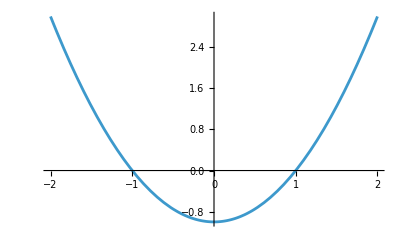

```mathematica
Plot[f[x], {x, -2, 2}]
```

```mathematica
r[x_, t_] = x + t^2 - 3;
```

```mathematica
Plot3D[r[x, t], {x, -1, 1}, {t, 0, 2}]
```

-Graphics3D-

```mathematica
Sqrt[4]
```

```mathematica
2
```

2

```mathematica
E^2
```

ⅇ^2

```mathematica
Exp[x]
```

ⅇ^x

```mathematica
Log[E]
```

1

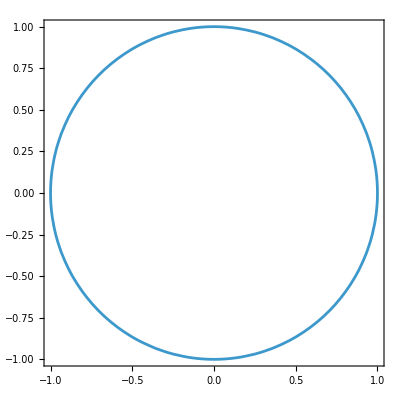

Plot::nonopt: Options expected (instead of {y,1,-1}) beyond position 2 in Plot[x^2+y^2==1,{x,-1,1},{y,1,-1}]. An option must be a rule or a list of rules.

Plot[x^2+y^2==1,{x,-1,1},{y,1,-1}]

```mathematica
ContourPlot[x^2+y^2==1,{x,-1,1},{y,-1,1}]
```

```mathematica
Log[10, 1]
```

0

```mathematica
Log[2, 4]
```

2

```mathematica
f[x_]:=Sinh[x];
N[f[2], 6]
```

3.62686

```mathematica
Power[3.4, 3]
```

39.304

```mathematica
Floor[2.34]
```

2

```mathematica
Ceiling[2.34]
```

3

```mathematica
Abs[-43]
```

43

```mathematica
Abs[2+3I]
```

√13

```mathematica
Sign[-4]
```

-1

```mathematica
Round[3.4]
```

3

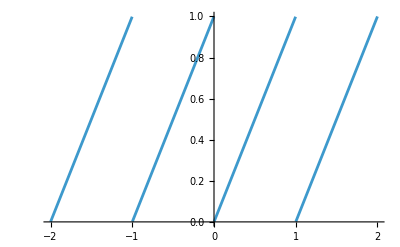

```mathematica
Plot[x - Floor[x], {x, -2, 2}]
```

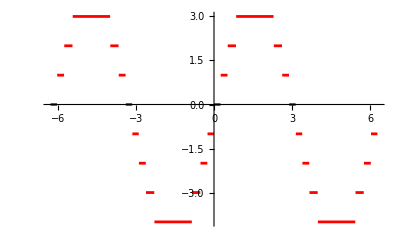

```mathematica
Plot[Floor[Sin[x]*4],{x, -2*Pi, 2*Pi} , PlotStyle-> Red]
```

```mathematica
Prime[411] (* give the n'th prime number*)
```

2833

```mathematica
PrimeQ[113] (* check if a numbert is prime *)
```

True

```mathematica
PrimeQ[12]
```

False

```mathematica
FactorInteger[456] (*return the factors of a number as a tree*)
(* (2*3)*(3,1)*(19,1) *)
```

{{2,3},{3,1},{19,1}}

```mathematica
GCD[10, 25] (* Greatest common divisor *)
```

5

```mathematica
LCM[10, 25] (* Least common multiply*)
```

50

```mathematica
Divisors[26] (* returns the number 1 to n that divide the number n*)
```

{1,2,13,26}

```mathematica
s = Solve[x^2 - 1==x, x]
```

{{x→1/2 (1-√5)},{x→1/2 (1+√5)}}

```mathematica
A=x/.s
```

{1/2 (1-√5),1/2 (1+√5)}

```mathematica
x1=A[[1]]
x2=A[[2]]
```

1/2 (1-√5)

1/2 (1+√5)

```mathematica
s[[1]]
```

{x→1/2 (1-√5)}

```mathematica
s[[1]][[1]](* it will return the first elemnt that it self is two part, before -> and after ->*)
```

```mathematica
x->1/2 (1-√5)
```

x→1/2 (1-√5)

```mathematica
s[[1]][[1]][[2]]
```

```mathematica
1/2 (1-√5)
```

1/2 (1-√5)

```mathematica
A={2, 4, -1, 7, 3}
```

{2,4,-1,7,3}

```mathematica
d=Length[A]
```

5

```mathematica
max=A[[1]]
```

```mathematica
2
```

2

```mathematica
(*Maximum Value of a List*)
```

```mathematica
A={3,7,2,9,5}; (*Example list*)
d=Length[A]; (*Length of the list*)
maxim=A[[1]]; (*Initialize max with the first element of the list*)

Do[If[A[[i]]>maxim,maxim=A[[i]]],{i,1,d}];

maxim(*Output the maximum value*)
```

9

```mathematica
findMax[A_]:=Module[{max,d,i},d=Length[A];(*Length of the list*)
maxim=A[[1]];(*Initialize max with the first element of the list*)
Do[If[A[[i]]>maxim,maxim=A[[i]]],{i,1,d}];
maxim(*Return the maximum value*)]


A={N[Power[Pi^E], 10],N[Power[E^Pi], 10], 6.78};
maxValue=findMax[A]
MaxValue
```

23.14069263

MaxValue

```mathematica
(*Find the root*)
```

Iteration 0: x = 2.18393

Iteration 1: x = 1.96339

Iteration 2: x = 1.81558

Iteration 3: x = 1.71722

Iteration 4: x = 1.65438

Iteration 5: x = 1.61647

Iteration 6: x = 1.5949

Iteration 7: x = 1.58322

Iteration 8: x = 1.57711

Iteration 9: x = 1.57398

Iteration 10: x = 1.5724

Iteration 11: x = 1.5716

Iteration 12: x = 1.5712

Iteration 13: x = 1.571

Iteration 14: x = 1.5709

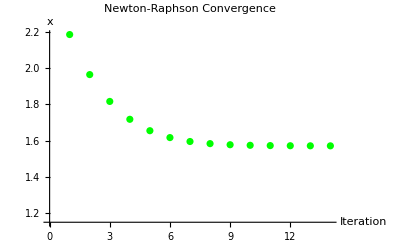

```mathematica
(*Define the function and its derivative*)
f[x_]:=Power[Cos[x], 2] * ( x^ 4 + 3x^3 - 4);

(*Derivative of f(x)*)
df[x_]=D[f[x],x]; 

(*Initial guess-choose a value where f'(x) is not zero*)
x[0]=0.2; (*Example:x[0]=0.5*)

(*Newton-Raphson iteration*)
Do[If[df[x[n]]==0,Print["Derivative is zero. Stopping iteration."];
Break[]];
x[n+1]=N[x[n]-f[x[n]]/df[x[n]]];

(*Update x[n+1]*)
Print["Iteration ",n,": x = ",N[x[n+1]]],(*Print the result*){n,0,14}]

(*Plot the convergence*)
ListPlot[Table[{i,x[i]},{i,0,14}],PlotStyle-> Green,AxesLabel->{"Iteration","x"},PlotLabel->"Newton-Raphson Convergence"]
```

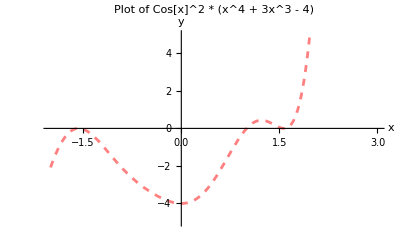

```mathematica
Plot[Cos[x]^2*(x^4+3 x^3-4),{x,-2,3},PlotStyle->{Pink,Dashed},AxesLabel->{"x","y"},PlotLabel->"Plot of Cos[x]^2 * (x^4 + 3x^3 - 4)",PlotRange->{{-2,3},{-5,5}}] (*Set y-range from-1 to 1*)
```

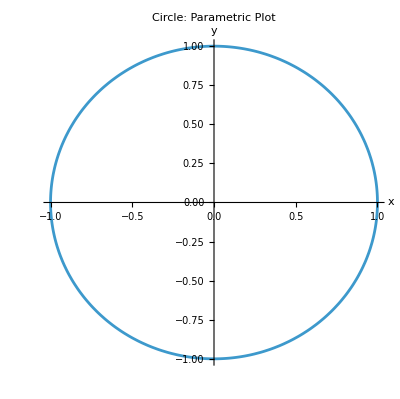

```mathematica
ParametricPlot[{Cos[θ],Sin[θ]},{θ,0,2 Pi},AxesLabel->{"x","y"},PlotLabel->"Circle: Parametric Plot",AspectRatio->Automatic]
```